```mathematica
h[x_,y_,p_,q_,ω_,k_,λ_]:=1/2(p^2+m^2/x^2+q^2+ω^2 x^2+k^2 y^2+λ/(√(x^2+y^2)));
```

```mathematica
D[h[x,y,p,q,ω,k,λ],x]
```

1/2 (-(2 m^2)/x^3-(x λ)/((x^2+y^2)^(3/2))+2 x ω^2)

```mathematica
D[h[x,y,p,q,ω,k,λ],y]
```

1/2 (2 k^2 y-(y λ)/((x^2+y^2)^(3/2)))

```mathematica
h[x_,y_,p_,q_,m_,w_,k_,wL_] := 1/(x + y)(2(x * p^2 + y*q^2) +m^2/2(1/x +1/y) + w^2/8(x^3+y^3)+ 2k) - wL*m ;
D[h[x,y,p,q,m,w,k,wL],x]
```

(2 p^2-m^2/(2 x^2)+(3 w^2 x^2)/8)/(x+y)-(2 k+1/2 m^2 (1/x+1/y)+2 (p^2 x+q^2 y)+1/8 w^2 (x^3+y^3))/(x+y)^2

```mathematica
Simplify[(2 p^2-m^2/(2 x^2)+(3 w^2 x^2)/8)/(x+y)-(2 k+1/2 m^2 (1/x+1/y)+2 (p^2 x+q^2 y)+1/8 w^2 (x^3+y^3))/(x+y)^2]
```

1/8 (w^2 (2 x-y)-(4 m^2)/(x^2 y)-(16 (k-p^2 y+q^2 y))/(x+y)^2)

```mathematica
Expand[1/8 (w^2 (2 x-y)-(4 m^2)/(x^2 y)-(16 (k-p^2 y+q^2 y))/(x+y)^2)]
```

(w^2 x)/4-m^2/(2 x^2 y)-(w^2 y)/8-(2 k)/(x+y)^2+(2 p^2 y)/(x+y)^2-(2 q^2 y)/(x+y)^2

```mathematica
Manipulate[Plot3D[1/8 (w^2 (2 x-y)-(4 m^2)/(x^2 y)-(16 (k-p^2 y+q^2 y))/(x+y)^2),{x,-8,8},{y,-8,8}],{k,-2,2},{m,-2,2},{p,-2,2},{q,-2,2},{w,-2,2}]
```

```mathematica
D[h[x,y,p,q,m,w,k,wL],y]
```

(2 q^2-m^2/(2 y^2)+(3 w^2 y^2)/8)/(x+y)-(2 k+1/2 m^2 (1/x+1/y)+2 (p^2 x+q^2 y)+1/8 w^2 (x^3+y^3))/(x+y)^2

```mathematica
Simplify[(2 q^2-m^2/(2 y^2)+(3 w^2 y^2)/8)/(x+y)-(2 k+1/2 m^2 (1/x+1/y)+2 (p^2 x+q^2 y)+1/8 w^2 (x^3+y^3))/(x+y)^2]
```

1/8 (-(4 m^2)/(x y^2)+(-16 k-16 p^2 x+16 q^2 x-w^2 x^3+3 w^2 x y^2+2 w^2 y^3)/(x+y)^2)

```mathematica
Manipulate[Plot3D[1/8 (-(4 m^2)/(x y^2)+(-16 k-16 p^2 x+16 q^2 x-w^2 x^3+3 w^2 x y^2+2 w^2 y^3)/(x+y)^2),{x,-8,8},{y,-8,8}],{k,-2,2},{m,-2,2},{p,-2,2},{q,-2,2},{w,-2,2}]
```

```mathematica
Manipulate[Plot3D[1/8 (-(4 m^2)/(x y^2)+(-16 k-16 p^2 x+16 q^2 x-w^2 x^3+3 w^2 x y^2+2 w^2 y^3)/(x+y)^2),{x,-8,8},{y,-8,8}],{k,-2,2},{m,-2,2},{p,-2,2},{q,-2,2},{w,-2,2},ContinuousAction->True,ImageMargins->Automatic,FrameMargins->None]
```

```mathematica
h[x_,y_,p_,q_,m_,w_,k_,wL_,d_] := 1/(d*(x-y))*(2(d*(x-1) * p^2 + d*(1-y)*q^2) +m^2/2*(1/(d*(x-1)) +1/(d*(1-y))) + w^2/8*(d*(x-1))^3+(d*(1-y))^3+ 2*k) - wL*m ;
```

```mathematica
D[h[x,y,p,q,m,w,k,wL,d],p]
```

(4 p (-1+x))/(x-y)

```mathematica
D[h[x,y,p,q,m,w,k,wL,d],q]
```

(4 q (1-y))/(x-y)

```mathematica
D[h[x,y,p,q,m,w,k,wL,d],x]
```

-(2 k+1/8 d^3 w^2 (-1+x)^3+1/2 m^2 (1/(d (-1+x))+1/(d (1-y)))+2 (d p^2 (-1+x)+d q^2 (1-y))+d^3 (1-y)^3)/(d (x-y)^2)+(2 d p^2-m^2/(2 d (-1+x)^2)+3/8 d^3 w^2 (-1+x)^2)/(d (x-y))

```mathematica
Simplify[-(2 k+1/8 d^3 w^2 (-1+x)^3+1/2 m^2 (1/(d (-1+x))+1/(d (1-y)))+2 (d p^2 (-1+x)+d q^2 (1-y))+d^3 (1-y)^3)/(d (x-y)^2)+(2 d p^2-m^2/(2 d (-1+x)^2)+3/8 d^3 w^2 (-1+x)^2)/(d (x-y))]
```

(-2 k+1/8 d^3 (w^2 (-1+x)^2 (1+2 x-3 y)+8 (-1+y)^3)+(m^2 (x-y)^2)/(2 d (-1+x)^2 (-1+y))-2 d (p^2-q^2) (-1+y))/(d (x-y)^2)

```mathematica
D[h[x,y,p,q,m,w,k,wL,d],y]
```

(2 k+1/8 d^3 w^2 (-1+x)^3+1/2 m^2 (1/(d (-1+x))+1/(d (1-y)))+2 (d p^2 (-1+x)+d q^2 (1-y))+d^3 (1-y)^3)/(d (x-y)^2)+(-2 d q^2+m^2/(2 d (1-y)^2)-3 d^3 (1-y)^2)/(d (x-y))

```mathematica
Simplify[(2 k+1/8 d^3 w^2 (-1+x)^3+1/2 m^2 (1/(d (-1+x))+1/(d (1-y)))+2 (d p^2 (-1+x)+d q^2 (1-y))+d^3 (1-y)^3)/(d (x-y)^2)+(-2 d q^2+m^2/(2 d (1-y)^2)-3 d^3 (1-y)^2)/(d (x-y))]
```

(2 k+2 d (p^2-q^2) (-1+x)+1/8 d^3 (w^2 (-1+x)^3-8 (-1+3 x-2 y) (-1+y)^2)+(m^2 (x-y)^2)/(2 d (-1+x) (-1+y)^2))/(d (x-y)^2)

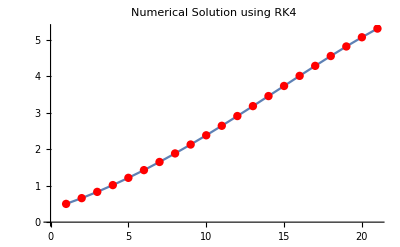

```mathematica
RK4[f_,{t0_,y0_},{tf_,h_}]:=Module[{t=t0,y=y0,k1,k2,k3,k4},NestWhileList[(k1=h*f[t,#];
k2=h*f[t+h/2,#+k1/2];
k3=h*f[t+h/2,#+k2/2];
k4=h*f[t+h,#+k3];
t=t+h;
#+(k1+2 k2+2 k3+k4)/6)&,y,t<tf&]]

(*Example usage*)
f[t_,y_]:=y-t^2+1;(*Example ODE:y'=y-t^2+1*)t0=0;(*Initial time*)y0=0.5;(*Initial value of y at t0*)tf=2;(*Final time*)h=0.1;(*Step size*)sol=RK4[f,{t0,y0},{tf,h}];
(*Applying RK4*)
ListLinePlot[sol,Mesh->All,MeshStyle->Red,PlotLabel->"Numerical Solution using RK4"]
```